```mathematica
Needs["DifferentialEquations`NDSolveProblems`"];
Needs["DifferentialEquations`NDSolveUtilities`"];
```

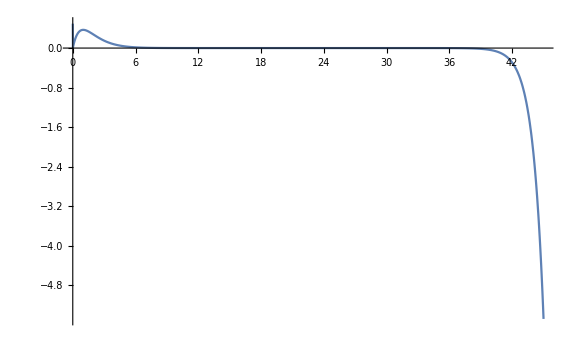

InterpolatingFunction::dmval: Input value {2540.} lies outside the range of data in the interpolating function. Extrapolation will be used.

General::stop: Further output of InterpolatingFunction::dmval will be suppressed during this calculation.

FindMinValue::sdprec: Line search unable to find a sufficient decrease in the function value with MachinePrecision digit precision.

-1.00135×10^151

FindMinValue::lstol: The line search decreased the step size to within the tolerance specified by AccuracyGoal and PrecisionGoal but was unable to find a sufficient decrease in the function. You may need more than MachinePrecision digits of working precision to meet these tolerances.

0.265832

```mathematica
s=NDSolve[{y''[x]==y[x]*((-2/(x))*Exp[-0*x]-2*(-0.49990011528759767386)),y[0.00005]==0,y'[0.00005]==1 },y,{x,0.00005,300}];
Plot[Evaluate[y[x]/.s],{x,0,45},PlotRange->All,ImageSize->Large]
FindMinValue[y[x]/.s,{x,20}]
```

```mathematica
ClassicalRungeKuttaCoefficients[4,prec_]:=With[{amat={{1/2},{0,1/2},{0,0,1}},bvec={1/6,1/3,1/3,1/6},cvec={1/2,1/2,1}},N[{amat,bvec,cvec},prec]]
```

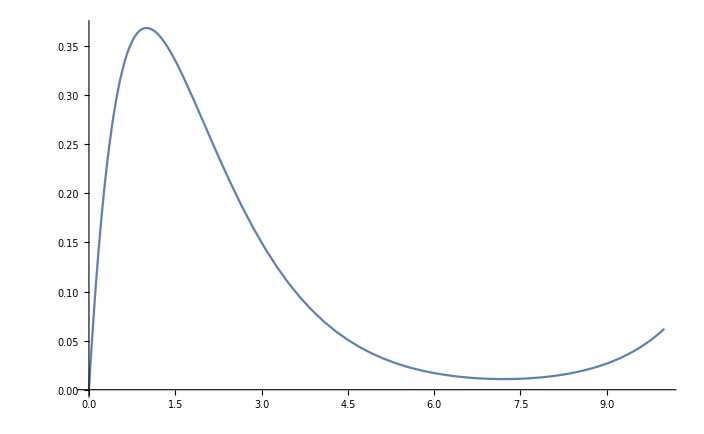

0.0108741

```mathematica
sol = NDSolve[{z''[x]==z[x]*((-2/(x))*Exp[-0*x]-2*(-0.5)),z[0.00005]==0,z'[0.00005]==1 },z,{x,0.00005,300},Method->{"ExplicitRungeKutta","DifferenceOrder"->4,"Coefficients"->ClassicalRungeKuttaCoefficients},StartingStepSize->5/10000];
Plot[z[t]/.sol,{t,0,10}]
FindMinValue[z[x]/.sol,{x,5}]
```